## dSigmadW - ep -> e p tau tau - Elastic

### Krzysztof Piotrzkowsk; Phys. Rev. D 63 (2001) 071502, Equation (1) EPA; Phys. Rept. 15 (1975) 181-281, Equations (6.16-6.17)

#### dn(ω) = ∫_(q_min^2)^(q_max^2) dn(ω, q^2) = N(ω) dω/ω; N (ω) = ∫_(q_min^2)^(q_max^2) dn(ω, q^2) dq^2/q^2;

Photon spectrum for Electron

```mathematica
Clear["Global`*"]
```

```mathematica
α=1/137;
me=0.000511;  (* Mass of electron in GeV *)
Ee = 50;             (* Energy of electron beam in GeV *)
FEe = 1;
FMe =1;

q2mine[ye_]:=(me^2  ye^2)/(1-ye);  
q2maxe= 10;
```

```mathematica
PhotonFluxElectron[ye_?NumericQ,prec_:MachinePrecision]:=1/ye* α/π*NIntegrate[((1-ye)(1-q2mine[ye]/q2)FEe +  ye^2/2 FMe) 1/q2 ,{q2,q2mine[ye],q2maxe}, MaxRecursion -> 100];  (* //Simplify *)
```

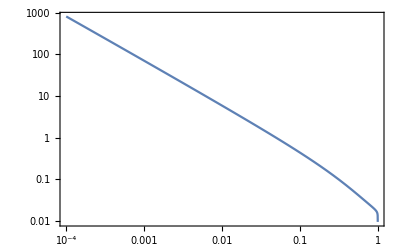

```mathematica
LogLogPlot[PhotonFluxElectron[ye],{ye,0.0001,0.9999},PlotRange->Full,Frame->True]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

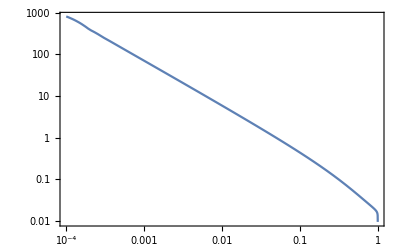

```mathematica
PhotonFluxElectronList=ParallelTable[Flatten[{ye, PhotonFluxElectron[ye]}],{ye,0.0001,0.9999,0.0001}];
funPhotonFluxElectronList=Interpolation[PhotonFluxElectronList]
PhotonFluxElectronFinal=FunctionInterpolation[funPhotonFluxElectronList[ye],{ye,0.0001,0.9999}]
LogLogPlot[PhotonFluxElectronFinal[ye],{ye,0.0001,0.9999},Frame->True]
```

Photon spectrum for Proton (Elastic)

```mathematica
α=1/137;
mp=0.938;  (* Mass of proton in GeV *)
Ep= 7000;   (* Energy of proton beam in GeV *)


GE2[q2_]:=(1+q2/0.71)^{-4}; 
GM2[q2_]:=7.78*GE2[q2]; 

FE[q2_]:=(4  mp^2  GE2[q2]+ q2  GM2[q2])/(4 mp^2 + q2);  (* Electric Form Factor *)
FM[q2_]:=GM2[q2];                                                                                     (* Magnetic Form Factor *)

Plot[FE[q2],{q2,1,1000},Frame->True];
Plot[FM[q2],{q2,1,1000},Frame->True];

q2minp[yp_]:=(mp^2  yp^2)/(1-yp);   (* For the case of elastic *)
q2maxp = 10;
```

```mathematica
PhotonFluxProton[yp_,prec_:MachinePrecision]:=1/yp*α/π*NIntegrate[((1-yp)(1-q2minp[yp]/q2)*FE[q2] +  yp^2/2 *FM[q2]) 1/q2 ,{q2,q2minp[yp],q2maxp}, MaxRecursion -> 100(*,PrecisionGoal->12,AccuracyGoal->15,WorkingPrecision->10*)];  (* //Simplify *)
```

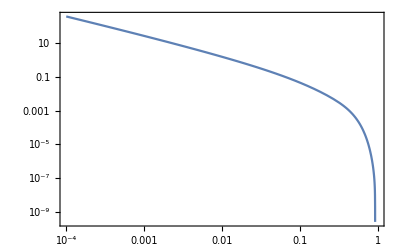

```mathematica
LogLogPlot[PhotonFluxProton[yp],{yp,0.0001,0.9999},PlotRange->Full,Frame->True]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

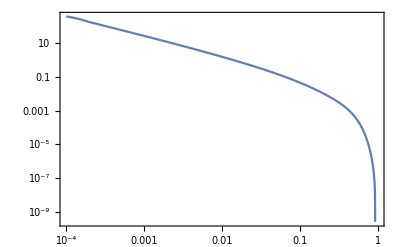

```mathematica
PhotonFluxProtonList=ParallelTable[Flatten[{yp, PhotonFluxProton[yp]}],{yp,0.0001,0.9999,0.0001}];
funPhotonFluxProtonList=Interpolation[PhotonFluxProtonList]
PhotonFluxProtonFinal=FunctionInterpolation[funPhotonFluxProtonList[yp],{yp,0.0001,0.9999}]
LogLogPlot[PhotonFluxProtonFinal[yp],{yp,0.0001,0.9999},Frame->True]
```

#### Elastic luminosity spectrum Syy at the LHeC Considering Eq.(1) of arXiv : 0908.2020 and (A .1) of our manuscript. My understanding is: Sgammagamma=2/W * (∫_(W^2/s)^1 ϕ(ye) ϕ(yp) yp ⅆye);

```mathematica
Ee = 50;
Ep=7000;

Sqrts= √(4 Ee Ep);                                  (* 1200 Center of mass energy in GeV *)

yp[ye_,W_]:=(W^2)/(ye  Sqrts^2);
Lowerlimit[W_]:=W^2/Sqrts^2 ;
```

```mathematica
Flux[ye_,W_]:=Re[PhotonFluxElectronFinal[ye] * PhotonFluxProtonFinal[yp[ye,W]]];
```

```mathematica
SgammagammaList=ParallelTable[Flatten[{W, 2/W*NIntegrate[Flux[ye,W] * yp[ye,W],{ye,Lowerlimit[W],1}, MaxRecursion -> 100]}],{W,10,1000,1}];
```

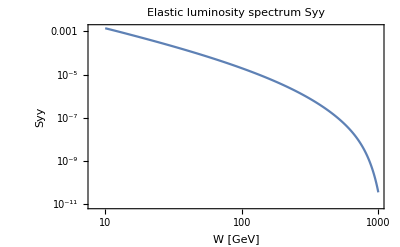

```mathematica
ListLogLogPlot[SgammagammaList,PlotRange->Full,PlotLabel->TraditionalForm["Elastic luminosity spectrum Syy"],Frame->True,FrameLabel->{"W [GeV]","Syy"},Joined->True]
```

```mathematica
Export["C:\\Users\\Hamzeh Khanpour\\Dropbox\\Photon_Photon_Interaction_LHC_LHeC\\OLD\\Mathematica_Final\\Syy-elastic-Q2-100000GeV2.dat",SgammagammaList]
```

C:\Users\Hamzeh Khanpour\Dropbox\Photon_Photon_Interaction_LHC_LHeC\OLD\Mathematica_Final\Syy-elastic-Q2-100000GeV2.dat

## Integrated Elastic luminosity spectrum Syy at the LHeC

```mathematica
fun=Interpolation[SgammagammaList]
```

InterpolatingFunction[…]

```mathematica
Sgg=FunctionInterpolation[fun[W],{W,10,1000}]
```

InterpolatingFunction[…]

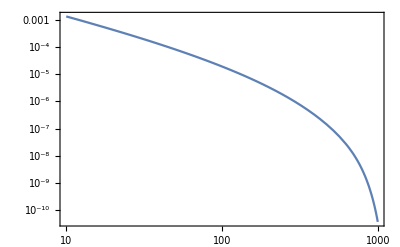

```mathematica
LogLogPlot[Sgg[W],{W,10,1000},Frame->True]
```

```mathematica
∫_W0^Sqrts Sgg[W]ⅆW
```

∫_W0^(200 √35) InterpolatingFunction[…][W]ⅆW

```mathematica
IntegratedSyy=ParallelTable[Flatten[{W0, NIntegrate[Sgg[W],{W,W0,1000}, MaxRecursion -> 100]}],{W0,10,1000,1}];
```

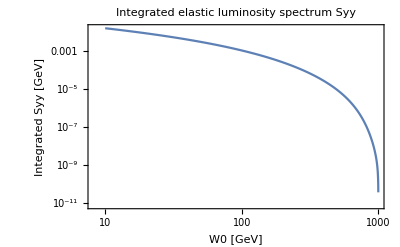

```mathematica
ListLogLogPlot[IntegratedSyy,PlotRange->Full,PlotLabel->TraditionalForm["Integrated elastic luminosity spectrum Syy"],Frame->True,FrameLabel->{"W0 [GeV]","Integrated Syy [GeV]"},Joined->True]
```

```mathematica
Export["C:\\Users\\Hamzeh Khanpour\\Dropbox\\Photon_Photon_Interaction_LHC_LHeC\\OLD\\Mathematica_Final\\Integrated-Syy-elastic-Q2-100000GeV2.dat",IntegratedSyy]
```

C:\Users\Hamzeh Khanpour\Dropbox\Photon_Photon_Interaction_LHC_LHeC\OLD\Mathematica_Final\Integrated-Syy-elastic-Q2-100000GeV2.dat

## dSigmadW - ep -> e p b bbar - Elastic case

```mathematica
csHiggsionos[wvalue_]:=Module[{mhiggsionos,hbarc2,alpha2,beta,cs},
mhiggsionos=1.77705;
hbarc2=0.389;
alpha2=(1.0/137.0)*(1.0/137.0);
(*Element-wise calculation of beta using If*)beta=Sqrt[If[1.0-4.0*mhiggsionos*mhiggsionos/wvalue^2.0>=0,1.0-4.0*mhiggsionos*mhiggsionos/wvalue^2.0,Indeterminate]];
(*Element-wise calculation of cs using If*)cs=If[wvalue>mhiggsionos,(4.0*π*alpha2*hbarc2)/wvalue^2.0*(beta)*((3.0-(beta^4.0))/(2.0*beta)*Log[(1.0+beta)/(1.0-beta)]-2.0+beta^2.0),0.]*10^9;
cs]

(*Example usage:*)
wvalue=1.77705;
result=csHiggsionos[wvalue]
```

0.

```mathematica
dSigmadW=ParallelTable[Flatten[{W, csHiggsionos[W] * Sgg[W]}],{W,10,1000,1}];
```

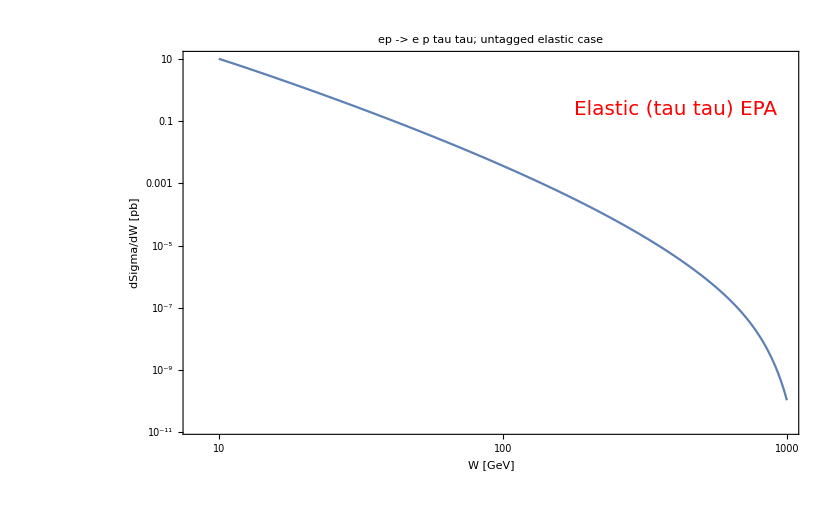

```mathematica
ListLogLogPlot[dSigmadW,PlotRange->Full,PlotLabel->TraditionalForm["ep -> e p tau tau; untagged elastic case"],Frame->True,FrameLabel->{"W [GeV]","dSigma/dW [pb]"},Joined->True,Epilog->{Text[Style["Elastic (tau tau) EPA",FontSize->20,Red],Scaled[{0.8,0.85}]]}]
```

```mathematica
Export["C:\\Users\\Hamzeh\\Dropbox\\Photon_Photon_Interaction_LHC_LHeC\\dSigmadY\\dSigmadW_ep_bbbar.pdf",%]
```

C:\Users\Hamzeh\Dropbox\Photon_Photon_Interaction_LHC_LHeC\dSigmadY\dSigmadW_ep_bbbar.pdf

ListLogLogPlot::prng: Value of option PlotRange -> {{1/10000,10000},{1/10000,10000},Automatic} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

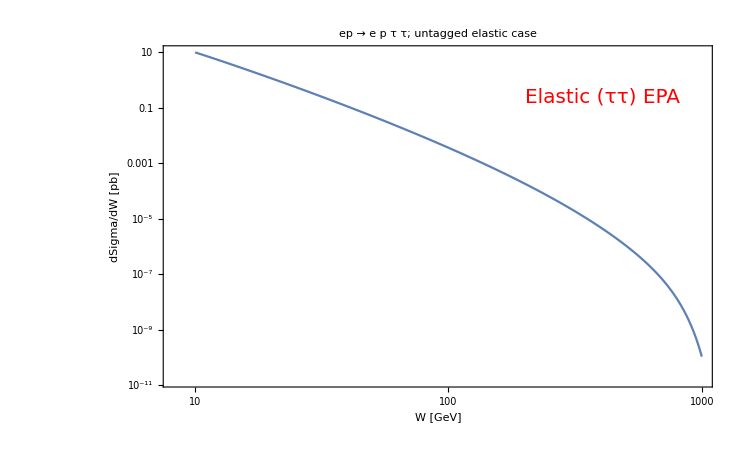

```mathematica
ListLogLogPlot[dSigmadW,PlotLabel->"ep → e p τ τ; untagged elastic case",Frame->True,FrameLabel->{"W [GeV]","dSigma/dW [pb]"},Joined->True,PlotRange->{{10^-4,10^4},{10^-4,10^4},Automatic},(*Set x-axis range from 10^-4 to 10^4*)Epilog->{Text[Style["Elastic (ττ) EPA",FontSize->20,Red],Scaled[{0.8,0.85}]]}]
```

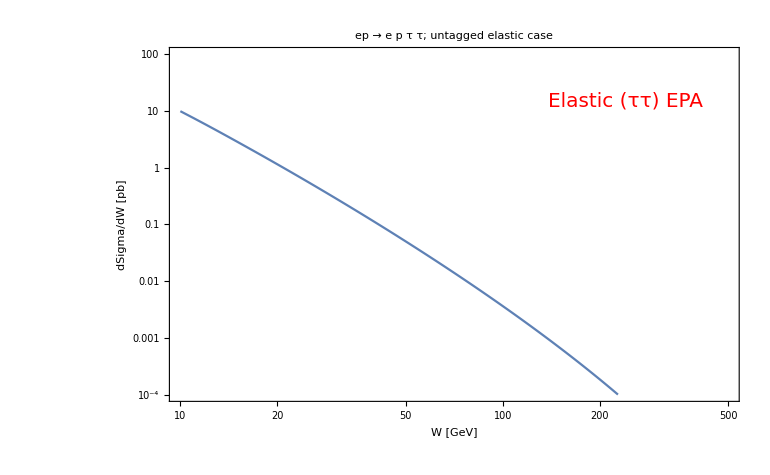

```mathematica
ListLogLogPlot[dSigmadW,PlotLabel->"ep → e p τ τ; untagged elastic case",Frame->True,FrameLabel->{"W [GeV]","dSigma/dW [pb]"},Joined->True,PlotRange->{{10,500},{10^-4,10^2}},(*Set range for both axes*)Epilog->{Text[Style["Elastic (ττ) EPA",FontSize->20,Red],Scaled[{0.8,0.85}]]}]
```